## Neutron Stars

## Units

```mathematica
G=667/100*10^-11; (*m^3 kg^-1 s^-2*)
```

```mathematica
Gcgs=667/100*10^-8; (*cm^3 g^-1 s^-2*)
```

```mathematica
c = 299792458; (*m s^-1*)
```

```mathematica
Msun = 1.989*10^30;(*kg*)
```

```mathematica
L = (Msun G)/c^2 10^-3;(*L=1.482 km*)
```

```mathematica
A=16/10  10^32; (*MeV/fm^3->J/m^3:MeV/fm^3(10^6 eV)/(1MeV)(1.6 x10^-19 J)/(1eV)((1fm)/(10^-15 m))^3*)
```

```mathematica
k=L^2 A G c^-4 10^6;(* MeV/fm^3 -> dimensionless *)
```

## Interpolation of EoS

Importing data from files

```mathematica
DataEOS = Import["/Users/carlosconde/Documents/Research/MUSES/NS_numerical_integrators/NS_Mathematica/eos.dat"];
```

Reading table: [ energy density, pressure ]

```mathematica
dataEoS = Transpose[{k*DataEOS[[All,3]], k*DataEOS[[All,2]]}];
```

Using monotonic interpolation to obtain P(ε) for each EoS

```mathematica
P=ResourceFunction["CubicMonotonicInterpolation"][dataEoS];
```

## TOV Integrator

```mathematica
Clear[TOVintegrator];
```

```mathematica
TOVintegrator[εc_,rc_,δ_]:=Module[{Rc,r,Eq1,Eq2,Eq3,Eqs,IC,ICnu,Sol,Solnu,ε,m,ν, εsol,msol,νsol,PLOTεsol,PLOTmsol,PLOTpsol, R,M,output},
Rc=rc/(10^5 L); 
Eq1=P'[ε[r]]ε'[r]==-(ε[r]+P[ε[r]]) (m[r]+4 Pi P[ε[r]] r^3)/(r (r-2 m[r]));
Eq2=m'[r]==4Pi ε[r] r^2;
Eqs={Eq1,Eq2};
IC={
ε[Rc]==εc-(2 Pi)/3 (εc+P[εc]) (εc+3 P[εc]) Rc^2,
m[Rc]==4Pi εc (Rc)^3/3,
WhenEvent[ε[r]==δ εc,{R=r,M=m[r]};"StopIntegration"]
};

Sol=NDSolve[{Eqs,IC},{ε,m},{r,Rc,50},AccuracyGoal->13,PrecisionGoal->13];

εsol=ε/.Sol[[1,1]];
msol=m/.Sol[[1,2]];

(* Solving for ν[r]*)
Eq3=ν'[r]==2*(msol[r]+4 Pi P[εsol[r]] r^3)/(r (r-2 msol[r]));
ICnu={ν[R]==Log[1-(2 M)/R]};
Solnu=NDSolve[{Eq3,ICnu},ν,{r,R,Rc},AccuracyGoal->13,PrecisionGoal->13];
νsol=ν/.Solnu[[1]];

output={εc/k,L*R,M,{εsol,msol,νsol,Rc,R,M},PLOTεsol,PLOTmsol,PLOTpsol}];
```

## TOV Plots

```mathematica
Clear[TOVplots];
```

```mathematica
TOVplots[εc_,rc_,δ_]:=Module[{TOVsol,εsol,msol,νsol,R,Rc,M,psol,PLOTεsol,PLOTmsol,PLOTpsol,PLOTνsol,PLOTνintext,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
R=TOVsol[[5]];
M=TOVsol[[6]];

PLOTεsol=Plot[εsol[r R]/εc,{r,Rc/R, 1}, 
PlotStyle->{Blue, Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18],Style["ϵ/ϵ_c",FontFamily->"Latin Modern Roman",FontSize->18]}];

PLOTmsol=Plot[msol[r R]/M,{r,Rc/R, 1},
PlotStyle->{RGBColor[.26,.58,0.], Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18],
Style["m/M",FontFamily->"Latin Modern Roman",FontSize->18]}];

PLOTpsol=Plot[P[εsol[r R]]/P[εc],{r,Rc/R, 1},
PlotStyle->{Red, Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18],Style["p/p_c",FontFamily->"Latin Modern Roman",FontSize->18]}];

PLOTνsol=Plot[νsol[r R],{r,Rc/R, 1}, 
PlotStyle->{Orange, Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["ν_int",FontFamily->"Latin Modern Roman",FontSize->18]},PlotRange->{{0,2.1},{-1,0}}];

PLOTνintext=Plot[Piecewise[{{νsol[r R],r<(L*R)/(L*R)},{Log[1-(2 M)/(r R)],r>(L*R)/(L*R)}}],{r,(L*Rc)/(L*R), (L*R+15)/(L*R)}(*,Epilog->Line[{{1,-100},{1,100}}]*),
PlotStyle->{Orange, Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["ν",FontFamily->"Latin Modern Roman",FontSize->18]},PlotRange->{{0,2.1},{-1,0}}];

output={PLOTεsol,PLOTmsol,PLOTpsol,PLOTνsol,PLOTνintext}];
```

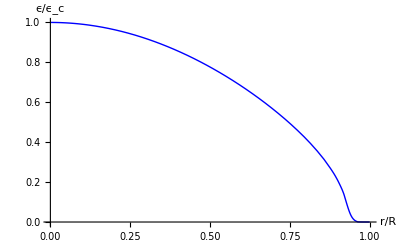
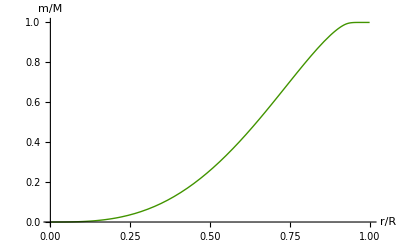
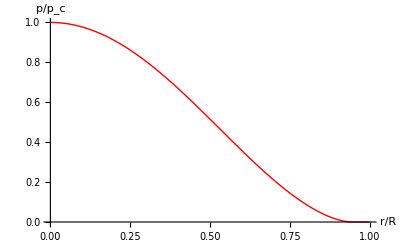
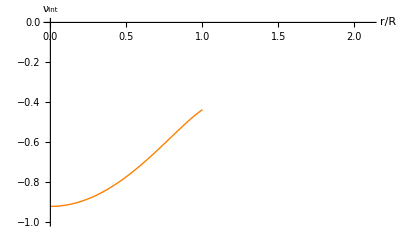
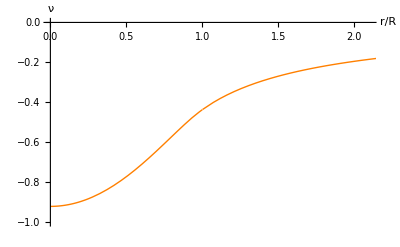

```mathematica
TOVplots[555*k,10,10^-8]
```

## M-R Curve

```mathematica
dataMR=Table[TOVintegrator[i*k,1,10^-8][[1;;3]], {i,150,2200,41}];(*From i=ϵc=140 MeV/fm^3to i=ϵc=2200 MeV/fm^3*)
```

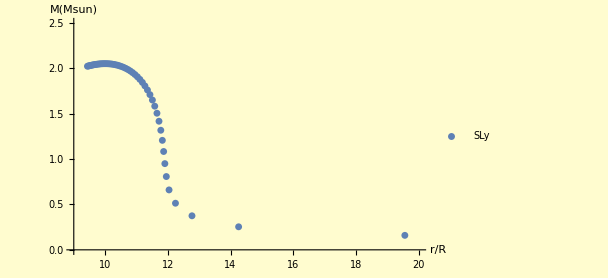

```mathematica
ListPlot[Transpose[{dataMR[[All,2]],dataMR[[All,3]]}],AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["M(Msun)",FontFamily->"Latin Modern Roman",FontSize->18]},LabelStyle->{GrayLevel[0]}, PlotRange->{{9,20},{0,2.5}},Background->RGBColor[1.,0.99,0.81],AxesStyle->Directive[Black, 14],ImageSize->450, PlotLegends->{"SLy"}]
```

## ω1 Integrator

```mathematica
Clear[ω1integrator];
```

```mathematica
ω1integrator[εc_,rc_,δ_,ωc_,Ωnew_]:=Module[{TOVsol,εsol,msol,νsol,r,R,Rc,M,I,Ω,Omega,ω1,Eq,ICω1,Solω1,ω1sol,ω1solnew,PLOTωintnew,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
R=TOVsol[[5]];
M=TOVsol[[6]];

(*SOLVING FOR ω1[r]*)
Eq=ω1''[r]+4 (1-Pi r^2(εsol[r]+P[εsol[r]])(1-(2 msol[r])/r)^-1)/r ω1'[r]-16Pi(εsol[r]+P[εsol[r]])(1-(2 msol[r])/r)^-1 ω1[r] ==0;
ICω1={ω1[Rc]==ωc+(8 Pi)/5(εc+P[εc])ωc Rc^2,ω1'[Rc]==(16 Pi)/5(εc+P[εc])ωc Rc};
Solω1=NDSolve[{Eq,ICω1},ω1,{r,Rc,R},AccuracyGoal->13,PrecisionGoal->13];
ω1sol=ω1/.Solω1[[1]];

(* Moment of Inertia *)

I = R^4/2( ω1sol'[R]/(R ω1sol'[R]+3 ω1sol[R]));

Ω = (R  ω1sol'[R])/3+ ω1sol[R];

(* Rescalling solution *)

ω1solnew[x_]:=ω1sol[x] (Ωnew/Ω);
Omega =(R  ω1solnew'[R])/3+ ω1solnew[R];

(*Plot of rescaled solution*)
PLOTωintnew=Plot[ω1solnew[r R],{r,Rc/R, 1}, 
PlotStyle->{Blue, Thick},AxesLabel->{Style["r/R",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["ω1",FontFamily->"Latin Modern Roman",FontSize->18]},PlotRange->Automatic, ImageSize->380,AxesStyle->Directive[Black, 14],PlotLabel->Style["ω1_new", FontSize->18]];

output={I,M,I/M^3,ω1sol,Ω ,PLOTωintnew}];
```

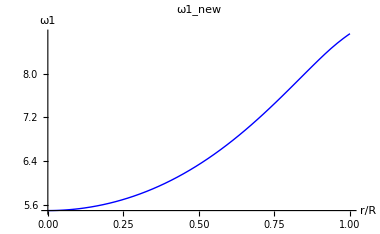
{31.7425,1.40578,11.4259,InterpolatingFunction[…],1.82056,-Graphics-}

```mathematica
ω1integrator[555*k,10,10^-8,1,10]
```

## I-M Curve

```mathematica
dataI=Table[ω1integrator[i*k,1,10^-8,1,10][[1;;2]], {i,150,2200,41}];
```

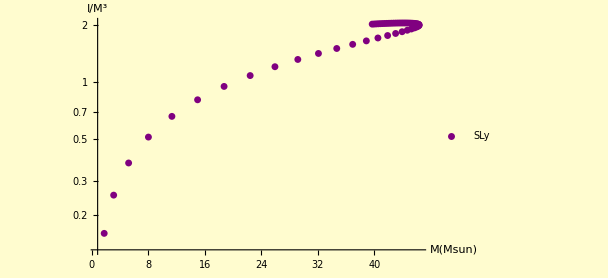

```mathematica
ListLogPlot[Transpose[{dataI[[All,1]],dataI[[All,2]]}],AxesLabel->{Style["M(Msun)",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["I/M^3",FontFamily->"Latin Modern Roman",FontSize->18]},LabelStyle->{GrayLevel[0]}, PlotRange->All,Background->RGBColor[1.,0.99,0.81],AxesStyle->Directive[Black, 14],ImageSize->450, PlotLegends->{"SLy"},PlotStyle->Purple]
```

## Tidal Deformability and Love Number

```mathematica
Clear[TidalIntegrator];
```

```mathematica
TidalIntegrator[εc_,rc_,δ_,l_]:=Module[{TOVsol,εsol,msol,R,Rc,f,A,B,Eq,IC,r,y,ysol,SolLove,Y,M,C,k2,k3,λ,λbar,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
Rc=TOVsol[[4]];
R=TOVsol[[5]];
M=TOVsol[[6]];

f=1-1/r 2 msol[r];
A=2/f(1-1/r 3 msol[r]-2 Pi r^2(εsol[r]+3 P[εsol[r]] ));
B=1/f(l(l+1)-4 Pi r^2(εsol[r]+P[εsol[r]] )(3+1/P'[εsol[r]]));  (* 1/P'[εsol[r]] *)

Eq=r y'[r]+y[r](y[r]-1)+A  y[r]-B ==0;

IC=y[Rc]==l;

SolLove=NDSolve[{Eq,IC},y,{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];
ysol=y/.SolLove[[1]];

Y=ysol[R];
C=M/R;

k2=8/5(1-2C)^2 C^5 *(2C *(Y-1)-Y+2)
(2C*(  4(Y+1)C^4 + (6 Y-4)C^3+(26-22Y)C^2+3(5Y-8)C-3Y+6 ) -3(1-2C)^2(2C*(Y-1)-Y+2) Log[1/(1-2C)])^-1;

λ=2/3 (k2 /Gcgs)( 10^5 L R)^5; (* cgs units *)
λbar=2/3 k2 C^-5;
output={L R,M,λ,k2,Y,λbar}];
```

## λ - M Curve

```mathematica
dataλ=Table[TidalIntegrator[i*k,10,10^-8,2][[2;;3]], {i,140,2200,41}];
```

```mathematica
ListPlot[Transpose[{dataλ[[All,1]],dataλ[[All,2]]}],AxesLabel->{Style["M [M_☉]",FontFamily->"Latin Modern Roman", FontSize->18]
,Style["λ [g cm^2s^2 ]",FontFamily->"Latin Modern Roman",FontSize->18]},LabelStyle->{GrayLevel[0]}, PlotRange->All,Background->RGBColor[1.,0.99,0.81],AxesStyle->Directive[Black, 14],ImageSize->450, PlotLegends->{"SLy"},PlotStyle->Purple]
```

-Graphics-

### Quadrupole Moment

```mathematica
Clear[QuadrupoleIntegrator];
```

```mathematica
QuadrupoleIntegrator[εc_,rc_,δ_,B_]:=Module[{TOVsol,OmegaInt,εsol,msol,νsol,ω1sol,R,M,I,Ibar,Rc,f,h2p,k2p,h2H,k2H,
              Eq1H,Eq2H,Eq1p,Eq2p,EqH,Eqp,ICp,ICH,SolH,Solp,a1,a2,a3,b1,b2,b3,h2Hsol,k2Hsol,h2psol,k2psol,
               h2Hint,k2Hint,h2pint,k2pint,h2Hext,k2Hext,h2pext,k2pext,r,A,qbar,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
(*Rc=SetPrecision[TOVsol[[4]],22];*)
R=TOVsol[[5]];
M=TOVsol[[6]];

OmegaInt=ω1integrator[εc,rc,δ,1.0,10];
I=OmegaInt[[1]];
Ibar=OmegaInt[[3]];
ω1sol=OmegaInt[[4]];

a1[r_]:=(2 (msol[r]^2-r^2+2 Pi r^4(P[εsol[r]]-8 Pi r^2 P[εsol[r]]^2+εsol[r])+ msol[r](r-4 Pi r^3(3 P[εsol[r]] + εsol[r] ))))/(r(r-2 msol[r] ) (msol[r]+4 Pi r^3 P[εsol[r]] ));

a2[r_]:=-2/(msol[r]+4 Pi r^3 P[εsol[r]]);

a3[r_]:=(4 E^(-νsol[r])Pi r^3(r^2+2 msol[r]^2+ 32 Pi^2 r^6 P[εsol[r]]^2+2 msol[r] r (8 Pi r^2 P[εsol[r]]-1) )(P[εsol[r]]+ εsol[r]))/(3(r-2 msol[r] ) (msol[r]+4 Pi r^3 P[εsol[r]] ))ω1sol[r]^2
            +(E^(-νsol[r])(2 msol[r] r^2(r+msol[r])-r^4+16 Pi r^5 msol[r]P[εsol[r]]+32 Pi^2 r^8 P[εsol[r]]^2))/(12 (msol[r]+4 Pi r^3 P[εsol[r]] ))ω1sol'[r]^2;

b1[r_]:=2/(msol[r]+4 Pi r^3 P[εsol[r]]);

b2[r_]:=(2 (r+msol[r]-2 Pi r^3 (P[εsol[r]]+εsol[r] )))/(r (msol[r]+4 Pi r^3 P[εsol[r]] ));

b3[r_]:=(4 E^(-νsol[r])Pi r^3(2 msol[r] - r + 8 Pi r^3 P[εsol[r]] )(P[εsol[r]]+ εsol[r]))/(3 (msol[r]+4 Pi r^3 P[εsol[r]] ))ω1sol[r]^2 
               + (E^(-νsol[r])r^2(r-2 msol[r] )(r+2 msol[r] + 8 Pi r^3 P[εsol[r]] ))/(12 (msol[r]+4 Pi r^3 P[εsol[r]] ))ω1sol'[r]^2;

Eq1H=h2H'[r]==a1[r] h2H[r]+ a2[r] k2H[r];
Eq2H=k2H'[r]==b1[r]k2H[r]+ b2[r]h2H[r];
EqH={Eq1H,Eq2H};
ICH={h2H[Rc]==B Rc^2,k2H[Rc]==-B Rc^2};
SolH=NDSolve[{EqH,ICH},{h2H,k2H},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];

Eq1p=h2p'[r]==a1[r] h2p[r]+ a2[r] k2p[r]+a3[r];
Eq2p=k2p'[r]==b1[r]k2p[r]+ b2[r]h2p[r]+ b3[r];
Eqp={Eq1p,Eq2p};
ICp={h2p[Rc]==B Rc^2,k2p[Rc]==-B Rc^2};                   
Solp=NDSolve[{Eqp,ICp},{h2p,k2p},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];
                           
h2Hsol=h2H/.SolH[[1,1]];
k2Hsol=k2H/.SolH[[1,2]];
h2psol=h2p/.Solp[[1,1]];
k2psol=k2p/.Solp[[1,2]];

h2Hint=h2Hsol[R];
k2Hint=k2Hsol[R];
h2pint=h2psol[R];
k2pint=k2psol[R];

h2pext[M_,R_,I_]:=1/(M R^3)(1+M/R)I^2;
h2Hext[M_,R_]:=-(3 R^2)/(M(R-2 M))(1-3 M/R+4/3(M/R)^2+2/3(M/R)^3+R/(2M)(1-(2M)/R)^2 Log[1-(2M)/R]) ;

k2pext[M_,R_,I_]:=-1/(M R^3)(1+(2M)/R)I^2;
k2Hext[M_,R_]:=(3 R)/M(1+M/R-2/3(M/R)^2+R/(2M)(1-(2 M^2)/R^2)Log[1-(2M)/R]);


A=((h2pext[M,R,I]-h2pint) k2Hint-(k2pext[M,R,I]-k2pint) h2Hint)/(h2Hint k2Hext[M,R] - h2Hext[M,R] k2Hint);
qbar=1+8/5 M^4/I^2 A;

output={ εc/k,L R,M,Ibar,qbar}];
```

```mathematica
QuadrupoleIntegrator2[εc_,rc_,δ_,B_]:=Module[{TOVsol,OmegaInt,εsol,msol,νsol,ω1sol,R,M,I,Ibar,Rc,f,h2p,k2p,h2H,k2H,
              Eq1H,Eq2H,Eq1p,Eq2p,EqH,Eqp,ICp,ICH,SolH,Solp,a1,a2,a3,b1,b2,b3,h2Hsol,k2Hsol,h2psol,k2psol,
               h2Hint,k2Hint,h2pint,k2pint,h2Hext,k2Hext,h2pext,k2pext,r,A,qbar,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
(*Rc=SetPrecision[TOVsol[[4]],22];*)
R=TOVsol[[5]];
M=TOVsol[[6]];

OmegaInt=ω1integrator[εc,rc,δ,1.0,10];
I=OmegaInt[[1]];
Ibar=OmegaInt[[3]];
ω1sol=OmegaInt[[4]];

Eq1H=h2H'[r]==(2*(-k2H[r] + (h2H[r]*(-r^2 + msol[r]^2 - 16*Pi^2*r^6*P[εsol[r]]^2 + 
                                           2*Pi*r^4*(P[εsol[r]] +εsol[r]) + msol[r]*(r - 4*Pi*r^3*(3*P[εsol[r]] + εsol[r]))))/
                                          (r*(r - 2*msol[r]))))/(msol[r] + 4*Pi*r^3*P[εsol[r]]);

Eq2H=k2H'[r]==(2*(r*k2H[r]+h2H[r]*(r+msol[r]-2*Pi*r^3*P[εsol[r]]-2*Pi*r^3*εsol[r])))
                         /(r*(msol[r]+4*Pi*r^3*P[εsol[r]]));

EqH={Eq1H,Eq2H};
ICH={h2H[Rc]==B Rc^2,k2H[Rc]==-B Rc^2};
SolH=NDSolve[{EqH,ICH},{h2H,k2H},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];


Eq1p=h2p'[r]==(1/(12*( msol[r] + 4*Pi*r^3*P[εsol[r]])))*(-24*k2p[r] + (1/(r*(r - 2*msol[r])))*
                                          (24*h2p[r]*(-r^2 + msol[r]^2 - 16*Pi^2*r^6*P[εsol[r]]^2 + 2*Pi*r^4*(P[εsol[r]] + εsol[r]) + 
                                           msol[r]*(r - 4*Pi*r^3*(3*P[εsol[r]] + εsol[r])))) + 
                                          (1/(r - 2*msol[r]))*((r^2*(16*Pi*r*(r^2 + 2*msol[r]^2 + 32*Pi^2*r^6*P[εsol[r]]^2 + 
                                           2*r*msol[r]*(-1 + 8*Pi*r^2*P[εsol[r]]))*(P[εsol[r]] +εsol[r])*ω1sol[r]^2 + 
                                          (r - 2*msol[r])*(2*msol[r]^2 + 2*msol[r]*(r + 8*Pi*r^3*P[εsol[r]]) + 
                                           r^2*(-1 + 32*Pi^2*r^4*P[εsol[r]]^2))*ω1sol'[r]^2))/E^νsol[r]));

Eq2p=k2p'[r]==(1/(12*(msol[r] + 4*Pi*r^3*P[εsol[r]])))*(24*k2p[r] + 
                                          (24*h2p[r]*(r + msol[r] - 2*Pi*r^3*(P[εsol[r]] + εsol[r])))/r + 
                                          (r^2*(16*Pi*r*(-r + 2*msol[r] + 8*Pi*r^3*P[εsol[r]])*(P[εsol[r]] + εsol[r])*ω1sol[r]^2 + 
                                          (r - 2* msol[r])*(r + 2* msol[r] + 8*Pi*r^3*P[εsol[r]])*ω1sol'[r]^2))/E^νsol[r]);
Eqp={Eq1p,Eq2p};
ICp={h2p[Rc]==B Rc^2,k2p[Rc]==-B Rc^2};                   
Solp=NDSolve[{Eqp,ICp},{h2p,k2p},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];
                           

h2Hsol=h2H/.SolH[[1,1]];
k2Hsol=k2H/.SolH[[1,2]];
h2psol=h2p/.Solp[[1,1]];
k2psol=k2p/.Solp[[1,2]];

h2Hint=h2Hsol[R];
k2Hint=k2Hsol[R];
h2pint=h2psol[R];
k2pint=k2psol[R];

h2pext[M_,R_,I_]:=1/(M R^3)(1+M/R)I^2;
h2Hext[M_,R_]:=-(3 R^2)/(M(R-2 M))(1-3 M/R+4/3(M/R)^2+2/3(M/R)^3+R/(2M)(1-(2M)/R)^2 Log[1-(2M)/R]) ;

k2pext[M_,R_,I_]:=-1/(M R^3)(1+(2M)/R)I^2;
k2Hext[M_,R_]:=(3 R)/M(1+M/R-2/3(M/R)^2+R/(2M)(1-(2 M^2)/R^2)Log[1-(2M)/R]);


A=((h2pext[M,R,I]-h2pint) k2Hint-(k2pext[M,R,I]-k2pint) h2Hint)/(h2Hint k2Hext[M,R] - h2Hext[M,R] k2Hint);
qbar=1+8/5 M^4/I^2 A;

output={ εc/k,L R,M,Ibar,qbar}];
```

```mathematica
QuadrupoleIntegrator[300 k,50,10^-8,1]
```

{300.,12.0886,0.609925,44.8143,30.3923}

```mathematica
QuadrupoleIntegrator2[300 k,50,10^-8,1]
```

{300.,12.0886,0.609925,44.8143,30.3923}

```mathematica
MonopoleIntegrator[εc_,rc_,δ_]:=Module[{TOVsol,OmegaInt,εsol,msol,νsol,ω1sol,R,M,I,Ω,Ibar,Rc,m0,m0sol,ξ0,ξ0sol,
              Eq1,Eq2,Eq,IC,Sol,δR,δM,r,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
R=TOVsol[[5]];
M=TOVsol[[6]];

OmegaInt=ω1integrator[εc,rc,δ,1.0,10];
I=OmegaInt[[1]];
Ibar=OmegaInt[[3]];
ω1sol=OmegaInt[[4]];
Ω=OmegaInt[[5]];

Eq1=m0'[r]== 1/12 E^(-νsol[r])r^3(32 Pi r ω1sol[r]^2(P[εsol[r]] + εsol[r]) + (r - 2 msol[r])ω1sol'[r]^2)-4 Pi r^2 ξ0[r]εsol'[r];

Eq2=ξ0'[r]==1/(12 ( 2msol[r]-r)r(msol[r]+4 Pi P[εsol[r]] r^3))E^(-νsol[r])(12 E^νsol[r](m0[r](r^2+ 8 Pi P[εsol[r]] r^4)+2ξ0[r](msol[r]^2-msol[r](r+8 Pi P[εsol[r]] r^3)+2Pi r^4(P[εsol[r]]+εsol[r]+8 Pi P[εsol[r]] r^2 εsol[r])))+r^3(r-2 msol[r])(8(3 msol[r]-r+4 Pi P[εsol[r]] r^3)ω1sol[r]^2-8 r (r-2 msol[r]) ω1sol[r]ω1sol'[r]-r^2(r-2 msol[r])ω1sol'[r]^2));

Eq={Eq1,Eq2};
IC={m0[Rc]==(8 E^(-νsol[Rc]))/5((2 Pi)/9(2εc + 3 P[εc] ) - 3/8 1/(εc+3P[εc])-1/P'[εsol[Rc]] 2/3 Pi (εc+P[εc])(εc+3 P[εc]))Rc^5
     ,ξ0[Rc]== (3 E^(-νsol[Rc]))/(8 Pi (εc+ 3 P[εc]))Rc };

Sol=NDSolve[{Eq,IC},{m0,ξ0},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];
                    
m0sol=m0/.Sol[[1,1]];
ξ0sol=ξ0/.Sol[[1,2]];

δM = m0sol[R] + (I Ω)^2/R^3 ;
δR = ξ0sol[R];

output={ εc/k,L R,M,L δR,δM,m0sol[R],(I Ω)^2/R^3 ,m0sol,ξ0sol}];
```

```mathematica
Clear[MonopoleIntegrator2];
```

```mathematica
MonopoleIntegrator2[εc_,rc_,δ_]:=Module[{TOVsol,OmegaInt,εsol,msol,νsol,ω1sol,λsol,j,R,M,I,Ω,Ibar,Rc,m0,m0sol,p0,p0sol,
              Eq1,Eq2,Eq,IC,Sol,δR,δM,r,output},

TOVsol=TOVintegrator[εc,rc,δ][[4]];
εsol=TOVsol[[1]];
msol=TOVsol[[2]];
νsol=TOVsol[[3]];
Rc=TOVsol[[4]];
R=TOVsol[[5]];
M=TOVsol[[6]];
λsol[x_]:=Log[x/(x-2 msol[x])];
j[x_]:=E^(-(νsol[x]+λsol[x])/2);

OmegaInt=ω1integrator[εc,rc,δ,0.058,10];
I=OmegaInt[[1]];
Ibar=OmegaInt[[3]];
ω1sol=OmegaInt[[4]];
Ω=OmegaInt[[5]];

Eq1=m0'[r]== 4 Pi r^2(εsol[r]+P[εsol[r]])/P'[εsol[r]] p0[r]+1/12 j[r]^2 r^4 ω1sol'[r]^2-1/3 r^3 D[j[r]^2,r] ω1sol[r]^2;

Eq2=p0'[r]==-4 Pi  ((εsol[r]+P[εsol[r]])r^2)/(r-2msol[r])p0[r]-(m0[r] r^2)/(r-2msol[r])^2(8Pi P[εsol[r]]+1/r^2)+1/12 r^4/(r-2 msol[r])j[r]^2 ω1sol'[r]^2+1/3 D[(r^3 j[r]^2 ω1sol[r]^2)/(r-2msol[r]),r];

Eq={Eq1,Eq2};
IC={m0[Rc]==(4 Pi)/15(εc+ 3 P[εc])(1/P'[εc]+2)(j[Rc]ω1sol[Rc])^2 Rc^5,p0[Rc]== 1/3(j[Rc]ω1sol[Rc])^2 Rc^2 };

Sol=NDSolve[{Eq,IC},{m0,p0},{r,Rc,R},AccuracyGoal->12,PrecisionGoal->12];
                    
m0sol=m0/.Sol[[1,1]];
p0sol=p0/.Sol[[1,2]];

δM = m0sol[R] + (I Ω)^2/R^3 ;
δR = (p0sol[R]R(R-2M))/M;

output={ εc/k,L R,M,L δR,δM,m0sol[R],(I Ω)^2/R^3 ,m0sol,p0sol}];
```

```mathematica
MonopoleIntegrator2[300 k,50,10^-8]
```

{300.,12.0886,0.609925,9.05794,0.916986,0.915973,0.00101267,InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
MonopoleIntegrator[300 k,50,10^-8]
```

{300.,12.0886,0.609925,2692.61,272.588,272.287,0.301031,InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
(*NOTE: The values of Q, δR, δM, depend on the choice of ωc. This is because ωc defines Ω*. This makes sense, the more angular speed the more mass-energy the star has and it is also more deformed. *)
```